# Analyze of A334671

The purpose of this note is to see if there are connections between this sequences and others in OEIS.

### Formula to get the sequence

```mathematica
(count = 1000;
AbsSumTravelIdNumber = {};
Do[(
a = Range[1,k];
m ={a};
Do[(
c ={};
b = Partition[a,k/2];
d = Reverse[b[[2]]];
Do[(
AppendTo[c,{b[[1,l]]}];
AppendTo[c,{d[[l]]}];
),{l,1,k/2,1}];
a = Flatten[c];
AppendTo[m,a];
),{n,1,k-1,1}];
idNumber = m[[All,2]];
absSum = 0;
Do[(
absSum += Abs[idNumber[[q]] - idNumber[[q+1]]];
),{q,1,Length[idNumber]-1,1}];
AppendTo[AbsSumTravelIdNumber, absSum];
),{k,2,count,2}];
Print[AbsSumTravelIdNumber];
)
```

{0,4,10,23,30,44,68,84,99,144,150,184,204,264,290,330,374,420,497,520,574,671,633,794,648,884,954,1080,1122,1248,1176,1116,1430,1577,1610,1785,1833,1880,1945,2183,2214,2324,2069,2550,2670,2880,3069,3040,2112,3300,3571,3662,3710,4145,3132,4332,4294,4529,4525,4760,4989,4699,4870,4031,5008,5764,5028,6120,6237,5576,7254,7014,6588,7212,7389,7799,7110,8060,7020,8566,8622,8856,8294,9326,7728,9901,10034,8369,10547,10740,11195,11224,11547,12069,11970,12224,7218,13069,13267,11418,13530,14052,13416,14519,14630,15071,14682,13140,12065,14724,16354,16871,13590,13983,17534,17864,18174,18000,18960,19120,18087,19764,20090,19461,19542,21084,21767,14669,22146,22703,22794,22176,21357,23836,24624,24840,24934,25094,22347,25771,26414,26270,27470,28235,26460,28590,28714,29399,28086,29900,27692,30704,31456,22316,31930,33537,30783,34384,32397,33948,31986,34884,29801,36378,36190,34241,37598,33484,38343,36432,26350,35928,41958,40832,39660,37200,41768,42452,42545,43080,28260,42012,40885,45716,43254,46004,42821,47000,45839,48582,43814,49087,24864,36408,51332,52005,51614,52813,45260,53716,53216,54671,53694,56211,35088,56444,56994,54576,57651,58660,59532,60396,60935,58721,61490,62064,63021,63035,64103,64823,64974,65564,66822,67910,67393,68519,68554,69620,60843,66336,70987,71835,72460,72476,70344,73637,74734,75839,76709,76859,71874,77924,78430,78501,81121,80524,77124,81840,81685,72209,83929,85549,66456,85750,86530,52530,82072,88580,82401,89960,90752,91872,94062,91674,87720,94164,94591,84479,97380,98054,97866,98464,99190,94040,102155,82156,100640,101639,103376,104904,105094,106738,105324,107310,107995,87114,110502,110400,103554,113232,117138,114071,114270,114963,108944,116828,117414,106704,119267,119474,116556,122707,123250,123783,123763,124644,120384,126280,110352,127625,127631,122897,122724,133604,132090,133560,129148,123745,134585,136320,137174,136617,138890,126287,137052,141484,142354,144132,145414,144980,145986,141036,145808,146634,143082,149973,146364,159492,156045,137805,156475,155724,133848,158577,157420,160079,125069,162325,127982,159828,164507,151979,165813,171101,161214,168744,169694,171711,165065,172560,112320,174484,175450,154430,172734,166466,169334,173340,181456,168936,183274,184264,178145,187954,187250,189317,188813,190260,166110,193474,193294,195071,195330,194138,88310,198404,137594,202601,200755,202540,197664,204624,205670,205944,207174,208824,210545,213274,210604,176690,213145,215204,205523,193874,218430,220320,217398,215284,140228,223928,224421,217991,229267,220692,200858,230464,231574,233519,234814,243102,222012,204334,239789,159392,231918,242368,235824,244255,242559,247202,249786,248997,227880,250356,250516,253187,254334,255193,150087,257840,263000,258503,267220,266507,240144,264924,266114,266378,271981,265210,228564,281070,263370,274824,277111,276944,263012,273288,280797,282744,258950,284284,293892,289817,287327,291884,290474,291720,293481,294220,294883,279882,258860,298760,286865,303376,303054,304751,303128,305921,238740,313276,310730,297294,314907,317045,304034,317200,316549,320783,291579,317654,230969,324246,326370,328680,329014,323925,317312,321828}

### The sequence

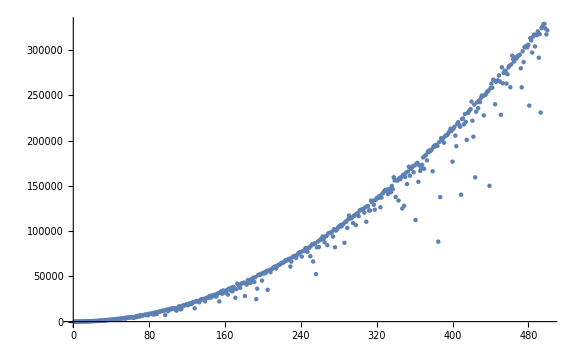

```mathematica
a334671 ={0,4,10,23,30,44,68,84,99,144,150,184,204,264,290,330,374,420,497,520,574,671,633,794,648,884,954,1080,1122,1248,1176,1116,1430,1577,1610,1785,1833,1880,1945,2183,2214,2324,2069,2550,2670,2880,3069,3040,2112,3300,3571,3662,3710,4145,3132,4332,4294,4529,4525,4760,4989,4699,4870,4031,5008,5764,5028,6120,6237,5576,7254,7014,6588,7212,7389,7799,7110,8060,7020,8566,8622,8856,8294,9326,7728,9901,10034,8369,10547,10740,11195,11224,11547,12069,11970,12224,7218,13069,13267,11418,13530,14052,13416,14519,14630,15071,14682,13140,12065,14724,16354,16871,13590,13983,17534,17864,18174,18000,18960,19120,18087,19764,20090,19461,19542,21084,21767,14669,22146,22703,22794,22176,21357,23836,24624,24840,24934,25094,22347,25771,26414,26270,27470,28235,26460,28590,28714,29399,28086,29900,27692,30704,31456,22316,31930,33537,30783,34384,32397,33948,31986,34884,29801,36378,36190,34241,37598,33484,38343,36432,26350,35928,41958,40832,39660,37200,41768,42452,42545,43080,28260,42012,40885,45716,43254,46004,42821,47000,45839,48582,43814,49087,24864,36408,51332,52005,51614,52813,45260,53716,53216,54671,53694,56211,35088,56444,56994,54576,57651,58660,59532,60396,60935,58721,61490,62064,63021,63035,64103,64823,64974,65564,66822,67910,67393,68519,68554,69620,60843,66336,70987,71835,72460,72476,70344,73637,74734,75839,76709,76859,71874,77924,78430,78501,81121,80524,77124,81840,81685,72209,83929,85549,66456,85750,86530,52530,82072,88580,82401,89960,90752,91872,94062,91674,87720,94164,94591,84479,97380,98054,97866,98464,99190,94040,102155,82156,100640,101639,103376,104904,105094,106738,105324,107310,107995,87114,110502,110400,103554,113232,117138,114071,114270,114963,108944,116828,117414,106704,119267,119474,116556,122707,123250,123783,123763,124644,120384,126280,110352,127625,127631,122897,122724,133604,132090,133560,129148,123745,134585,136320,137174,136617,138890,126287,137052,141484,142354,144132,145414,144980,145986,141036,145808,146634,143082,149973,146364,159492,156045,137805,156475,155724,133848,158577,157420,160079,125069,162325,127982,159828,164507,151979,165813,171101,161214,168744,169694,171711,165065,172560,112320,174484,175450,154430,172734,166466,169334,173340,181456,168936,183274,184264,178145,187954,187250,189317,188813,190260,166110,193474,193294,195071,195330,194138,88310,198404,137594,202601,200755,202540,197664,204624,205670,205944,207174,208824,210545,213274,210604,176690,213145,215204,205523,193874,218430,220320,217398,215284,140228,223928,224421,217991,229267,220692,200858,230464,231574,233519,234814,243102,222012,204334,239789,159392,231918,242368,235824,244255,242559,247202,249786,248997,227880,250356,250516,253187,254334,255193,150087,257840,263000,258503,267220,266507,240144,264924,266114,266378,271981,265210,228564,281070,263370,274824,277111,276944,263012,273288,280797,282744,258950,284284,293892,289817,287327,291884,290474,291720,293481,294220,294883,279882,258860,298760,286865,303376,303054,304751,303128,305921,238740,313276,310730,297294,314907,317045,304034,317200,316549,320783,291579,317654,230969,324246,326370,328680,329014,323925,317312,321828};
ListPlot[a334671]
```

### Analyzes

lookup 3 38 7 34 1 10 4 7 14 0 11 7 38 10 37 15 46 46 35 30 24 10 15 12 14  ->  No results.

```mathematica
countComp ={};
accu = 0;
Do[(
(*Print[a334671[[z]]];*)
If[
PrimeQ[a334671[[z]]],
(AppendTo[countComp,accu]; accu = 0),
accu++
];
),{z,1,Length[a334671],1}
];
Print[" "]
Print["Composit numbers between primes"]
Print[countComp]

FramedList = {}; 
Do[(
If[
PrimeQ[a334671[[n]]],
AppendTo[FramedList,Framed[a334671[[n]]]],
AppendTo[FramedList,a334671[[n]]]
];
),{n,1,Length[a334671],1}
];
Print[" "]
Print["Prime numbers in Framed List"]
Print[FramedList]

Column[Table[Binomial[i,j],{i,0,8},{j,0,i}],Center]
```

Composit numbers between primes

{3,38,7,34,1,10,4,7,14,0,11,7,38,10,37,15,46,46,35,30,24,10,15,12,14}

Prime numbers in Framed List

{0,4,10,23,30,44,68,84,99,144,150,184,204,264,290,330,374,420,497,520,574,671,633,794,648,884,954,1080,1122,1248,1176,1116,1430,1577,1610,1785,1833,1880,1945,2183,2214,2324,2069,2550,2670,2880,3069,3040,2112,3300,3571,3662,3710,4145,3132,4332,4294,4529,4525,4760,4989,4699,4870,4031,5008,5764,5028,6120,6237,5576,7254,7014,6588,7212,7389,7799,7110,8060,7020,8566,8622,8856,8294,9326,7728,9901,10034,8369,10547,10740,11195,11224,11547,12069,11970,12224,7218,13069,13267,11418,13530,14052,13416,14519,14630,15071,14682,13140,12065,14724,16354,16871,13590,13983,17534,17864,18174,18000,18960,19120,18087,19764,20090,19461,19542,21084,21767,14669,22146,22703,22794,22176,21357,23836,24624,24840,24934,25094,22347,25771,26414,26270,27470,28235,26460,28590,28714,29399,28086,29900,27692,30704,31456,22316,31930,33537,30783,34384,32397,33948,31986,34884,29801,36378,36190,34241,37598,33484,38343,36432,26350,35928,41958,40832,39660,37200,41768,42452,42545,43080,28260,42012,40885,45716,43254,46004,42821,47000,45839,48582,43814,49087,24864,36408,51332,52005,51614,52813,45260,53716,53216,54671,53694,56211,35088,56444,56994,54576,57651,58660,59532,60396,60935,58721,61490,62064,63021,63035,64103,64823,64974,65564,66822,67910,67393,68519,68554,69620,60843,66336,70987,71835,72460,72476,70344,73637,74734,75839,76709,76859,71874,77924,78430,78501,81121,80524,77124,81840,81685,72209,83929,85549,66456,85750,86530,52530,82072,88580,82401,89960,90752,91872,94062,91674,87720,94164,94591,84479,97380,98054,97866,98464,99190,94040,102155,82156,100640,101639,103376,104904,105094,106738,105324,107310,107995,87114,110502,110400,103554,113232,117138,114071,114270,114963,108944,116828,117414,106704,119267,119474,116556,122707,123250,123783,123763,124644,120384,126280,110352,127625,127631,122897,122724,133604,132090,133560,129148,123745,134585,136320,137174,136617,138890,126287,137052,141484,142354,144132,145414,144980,145986,141036,145808,146634,143082,149973,146364,159492,156045,137805,156475,155724,133848,158577,157420,160079,125069,162325,127982,159828,164507,151979,165813,171101,161214,168744,169694,171711,165065,172560,112320,174484,175450,154430,172734,166466,169334,173340,181456,168936,183274,184264,178145,187954,187250,189317,188813,190260,166110,193474,193294,195071,195330,194138,88310,198404,137594,202601,200755,202540,197664,204624,205670,205944,207174,208824,210545,213274,210604,176690,213145,215204,205523,193874,218430,220320,217398,215284,140228,223928,224421,217991,229267,220692,200858,230464,231574,233519,234814,243102,222012,204334,239789,159392,231918,242368,235824,244255,242559,247202,249786,248997,227880,250356,250516,253187,254334,255193,150087,257840,263000,258503,267220,266507,240144,264924,266114,266378,271981,265210,228564,281070,263370,274824,277111,276944,263012,273288,280797,282744,258950,284284,293892,289817,287327,291884,290474,291720,293481,294220,294883,279882,258860,298760,286865,303376,303054,304751,303128,305921,238740,313276,310730,297294,314907,317045,304034,317200,316549,320783,291579,317654,230969,324246,326370,328680,329014,323925,317312,321828}

### Sorted a334671

{0,4,10,23,30,44,68,84,99,144,150,184,204,264,290,330,374,420,497,520,574,633,648,671,794,884,954,1080,1116,1122,1176,1248,1430,1577,1610,1785,1833,1880,1945,2069,2112,2183,2214,2324,2550,2670,2880,3040,3069,3132,3300,3571,3662,3710,4031,4145,4294,4332,4525,4529,4699,4760,4870,4989,5008,5028,5576,5764,6120,6237,6588,7014,7020,7110,7212,7218,7254,7389,7728,7799,8060,8294,8369,8566,8622,8856,9326,9901,10034,10547,10740,11195,11224,11418,11547,11970,12065,12069,12224,13069,13140,13267,13416,13530,13590,13983,14052,14519,14630,14669,14682,14724,15071,16354,16871,17534,17864,18000,18087,18174,18960,19120,19461,19542,19764,20090,21084,21357,21767,22146,22176,22316,22347,22703,22794,23836,24624,24840,24864,24934,25094,25771,26270,26350,26414,26460,27470,27692,28086,28235,28260,28590,28714,29399,29801,29900,30704,30783,31456,31930,31986,32397,33484,33537,33948,34241,34384,34884,35088,35928,36190,36378,36408,36432,37200,37598,38343,39660,40832,40885,41768,41958,42012,42452,42545,42821,43080,43254,43814,45260,45716,45839,46004,47000,48582,49087,51332,51614,52005,52530,52813,53216,53694,53716,54576,54671,56211,56444,56994,57651,58660,58721,59532,60396,60843,60935,61490,62064,63021,63035,64103,64823,64974,65564,66336,66456,66822,67393,67910,68519,68554,69620,70344,70987,71835,71874,72209,72460,72476,73637,74734,75839,76709,76859,77124,77924,78430,78501,80524,81121,81685,81840,82072,82156,82401,83929,84479,85549,85750,86530,87114,87720,88310,88580,89960,90752,91674,91872,94040,94062,94164,94591,97380,97866,98054,98464,99190,100640,101639,102155,103376,103554,104904,105094,105324,106704,106738,107310,107995,108944,110352,110400,110502,112320,113232,114071,114270,114963,116556,116828,117138,117414,119267,119474,120384,122707,122724,122897,123250,123745,123763,123783,124644,125069,126280,126287,127625,127631,127982,129148,132090,133560,133604,133848,134585,136320,136617,137052,137174,137594,137805,138890,140228,141036,141484,142354,143082,144132,144980,145414,145808,145986,146364,146634,149973,150087,151979,154430,155724,156045,156475,157420,158577,159392,159492,159828,160079,161214,162325,164507,165065,165813,166110,166466,168744,168936,169334,169694,171101,171711,172560,172734,173340,174484,175450,176690,178145,181456,183274,184264,187250,187954,188813,189317,190260,193294,193474,193874,194138,195071,195330,197664,198404,200755,200858,202540,202601,204334,204624,205523,205670,205944,207174,208824,210545,210604,213145,213274,215204,215284,217398,217991,218430,220320,220692,222012,223928,224421,227880,228564,229267,230464,230969,231574,231918,233519,234814,235824,238740,239789,240144,242368,242559,243102,244255,247202,248997,249786,250356,250516,253187,254334,255193,257840,258503,258860,258950,263000,263012,263370,264924,265210,266114,266378,266507,267220,271981,273288,274824,276944,277111,279882,280797,281070,282744,284284,286865,287327,289817,290474,291579,291720,291884,293481,293892,294220,294883,297294,298760,303054,303128,303376,304034,304751,305921,310730,313276,314907,316549,317045,317200,317312,317654,320783,321828,323925,324246,326370,328680,329014}

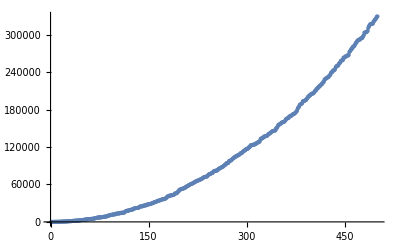

```mathematica
a334671Sorted = Sort[a334671]
ListPlot[a334671Sorted]
```

### Sorted composite numbers

searched on OEIS -> Nothing

```mathematica
compNrGapSorted = Sort[{3,38,7,34,1,10,4,7,14,0,11,7,38,10,37,15,46,46,35,30,24,10,15,12,14}];
compNrGapSorted
```

{0,1,3,4,7,7,7,10,10,10,11,12,14,14,15,15,24,30,34,35,37,38,38,46,46}